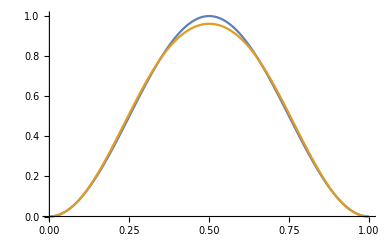

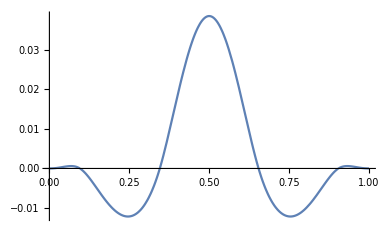

```mathematica
(*ФН 81426,
Диана Иванова, 2ра група, КН, трети курс*)

(*1.пресмятане на кубичен сплайн от вид пълна кубична интерполация*)
n=5;
f[t_]:= (Sin[π*t])^2; 
(*интерполационните възли*)
Do[x[i]=(Sin[(i*π)/(2*n)])^2, {i,0,n}];
(*разстояние между всеки два последователни възела*)
Do[Δ[i] = x[i+1]- x[i], {i,0,n-1}];

(*Съставяме система от поллиноми Pi(x), чиито коефициенти получаваме чрез метода на разделените разлики. За всеки два съседни възела, изчисляваме вторите прозводни на полинома Pi(x) и ги приравняваме после. Получената система решаваме по метода на прогонката *)
(*Изчисляваме коефициентите на системата*)
Do[systemA[i]=1/Δ[i-1],{i,1,n-1}];
Do[systemB[i]=2/Δ[i-1]+2/Δ[i],{i,1,n-1}];
Do[systemC[i]=1/Δ[i],{i,1,n-1}];
Do[systemValue[i]=3*(f[x[i]]-f[x[i-1]])/Δ[i-1]^2+3*(f[x[i+1]]-f[x[i]])/Δ[i]^2,{i,1,n-1}];

(*по метода на прогонката като намираме алфа и бета*)
alpha[1]=-systemC[1]/systemB[1];
beta[1]=systemValue[1]/systemB[1];
Do[alpha[i]=-systemC[i]/(systemA[i]*alpha[i-1]+systemB[i]),{i,2,n-2}];
Do[beta[i]=(systemValue[i]-systemA[i]*beta[i-1])/(systemA[i]*alpha[i-1]+systemB[i]),{i,2,n-1}];

(*от това че сплнайна ни е пълна кубична сплайн интерполация => директно изразяваме d[0] и d[n], където d1, d2... dn са решенията на системата *)
d[0] = f'[x[0]];
d[n] = f'[x[n]];

Do[d[i]=alpha[i]*d[i+1]+beta[i],{i,n-1,1,-1}];    (*обратен ход на прогонката*)
(*получаваме aCoef и bCoef чрез метода на разделените разлики*)
Do[aCoef[i]=d[i+1]/Δ[i]^2+d[i]/Δ[i]^2+2*(f[x[i]]-f[x[i+1]])/Δ[i]^3,{i,0,n-1}]; (*разделена разлика p[,,,]*)
Do[bCoef[i]=(f[x[i+1]]-f[x[i]])/Δ[i]^2-d[i]/Δ[i],{i,0,n-1}]; (*разделена разлика p[,,]*)
(*общ вид на полиномите интерполиращи f(t) във всеки подинтервал на [0, 1], определен от два последователни интерполационни възела *)
Do[polynomial[i,y_]=aCoef[i]*(y-x[i])^2*(y-x[i+1])+bCoef[i]*(y-x[i])^2+d[i]*(y-x[i])+f[x[i]],{i,0,n-1}];
(*кубичния сплайн за f(t) се получава като сума от полиномите интерполиращи f(t) за всеи подинтервал на [0,1]*)

cubicSpline[t_]:=Sum[If[t≥x[k]&&t≤x[k+1], polynomial[k, t], 0], {k, 0, n-1}];
(*2.визуализиране едновременно на графиките на функцията и кубичния сплайн*)
Plot[{f[t],cubicSpline[t]}, {t, 0, 1}, PlotPoints->300]
(*3.визуализиране на разликата на графиката на функцията и кубичния сплайн*)
Plot[f[t]-cubicSpline[t] , {t, 0, 1}, PlotRange-> All]
```